# Метод на разполовяването

Задача: Дадено ни е уравнението:
x^4-12 x^3 +77sinx- 32 = 0
1. Да се визуализира функцията
2. Да се определи броя на корените
3. Да се локализира един от тях 
4. Да се уточни локализирания корен по метода на разполовяването
5. Оценка на грешката
6. Колко итерации биха били необходими за достигане на точност 0.0001 по метода на разполовяването за избрания по време на локализацията интервал?

```mathematica
f[x_]:=x^4-12 x^3 +77Sin[x]-32
```

## 1. Да се визуализира функцията

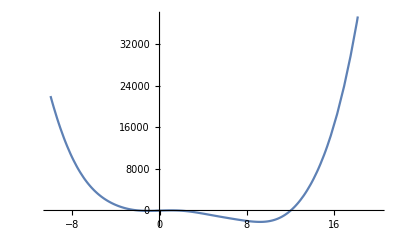

```mathematica
Plot[f[x],{x,-10,20}]
```

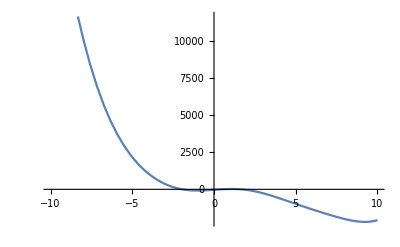

```mathematica
Plot[f[x],{x,-10,10}]
```

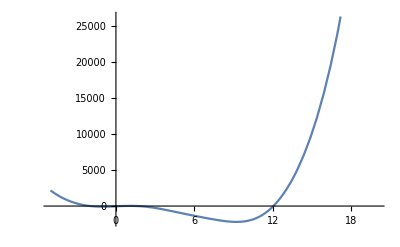

```mathematica
Plot[f[x],{x,-5,20}]
```

## 2. Да се определи броя на корените

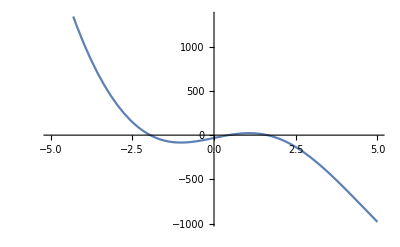

```mathematica
Plot[f[x],{x,-5,5}]
```

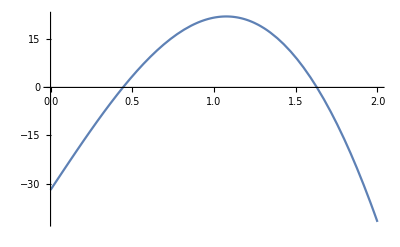

```mathematica
Plot[f[x],{x,0,2}]
```

## 3. Да се локализира един от тях

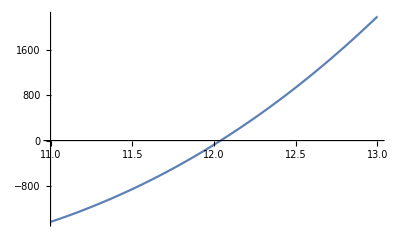

```mathematica
Plot[f[x],{x,11,13}]
```

```mathematica
f[11.]
```

-1440.

```mathematica
f[13.]
```

2197.35

Извод: 
(1) Функцията f(x) е непрекъсната, защото е сума от непрекъснати функции (полином и синус)
(2) f(11) = -1440 < 0
       f(13) = 2197.35.... > 0
       Функцията има различни знаци в двата края на разглеждания интервал [11; 13].
       Следователно от (1) и (2) следва, че в интервала [11; 13] функцията има поне един корен.

## 4. Да се уточни локализирания корен по метода на разполовяването

### Уточнение за съставяне на цикли и условни преходи

```mathematica
For[]
```

```mathematica
For[i=0,i<4,i++,Print[i]]
```

0

1

2

3

```mathematica
i
```

4

```mathematica
If[i<2,Print["малко"], Print["голямо"]]
```

голямо

```mathematica
For[i=0,i<4,i++,
(*тялото на цикъла*)
Print[i];
If[i<2,Print["малко"], Print["голямо"]]
]
```

0

малко

1

малко

2

голямо

3

голямо

### Съставяне на програмен код

#### основен код

```mathematica
f[x_]:=x^4-12 x^3 +77Sin[x]-32

For[
(*начални условия*)
n = 0; a = 11.;b=13.,
n<=3,n++,
(*тяло на цикъла*)
Print["n = ",n," a_n = ",a," b_n = ",b," m_n = ",m = (a+b)/2," f(m_n) = ",f[m]," ε_n = ",(b-a)/2];
If[f[m]<0,a=m,b=m]
]
```

n = 0 a_n = 11. b_n = 13. m_n = 12. f(m_n) = -73.3161 ε_n = 1.

n = 1 a_n = 12. b_n = 13. m_n = 12.5 f(m_n) = 939.456 ε_n = 0.5

n = 2 a_n = 12. b_n = 12.5 m_n = 12.25 f(m_n) = 403.61 ε_n = 0.25

n = 3 a_n = 12. b_n = 12.25 m_n = 12.125 f(m_n) = 157.928 ε_n = 0.125

```mathematica
f[12.]
```

-73.3161

#### с повече итерации

```mathematica
f[x_]:=x^4-12 x^3 +77Sin[x]-32

For[
(*начални условия*)
n = 0; a = 11.;b=13.,
n<=20,n++,
(*тяло на цикъла*)
Print["n = ",n," a_n = ",a," b_n = ",b," m_n = ",m = (a+b)/2," f(m_n) = ",f[m]," ε_n = ",(b-a)/2];
If[f[m]<0,a=m,b=m]
]
```

n = 0 a_n = 11. b_n = 13. m_n = 12. f(m_n) = -73.3161 ε_n = 1.

n = 1 a_n = 12. b_n = 13. m_n = 12.5 f(m_n) = 939.456 ε_n = 0.5

n = 2 a_n = 12. b_n = 12.5 m_n = 12.25 f(m_n) = 403.61 ε_n = 0.25

n = 3 a_n = 12. b_n = 12.25 m_n = 12.125 f(m_n) = 157.928 ε_n = 0.125

n = 4 a_n = 12. b_n = 12.125 m_n = 12.0625 f(m_n) = 40.5193 ε_n = 0.0625

n = 5 a_n = 12. b_n = 12.0625 m_n = 12.0313 f(m_n) = -16.8428 ε_n = 0.03125

n = 6 a_n = 12.0313 b_n = 12.0625 m_n = 12.0469 f(m_n) = 11.7269 ε_n = 0.015625

n = 7 a_n = 12.0313 b_n = 12.0469 m_n = 12.0391 f(m_n) = -2.58576 ε_n = 0.0078125

n = 8 a_n = 12.0391 b_n = 12.0469 m_n = 12.043 f(m_n) = 4.5636 ε_n = 0.00390625

n = 9 a_n = 12.0391 b_n = 12.043 m_n = 12.041 f(m_n) = 0.987181 ε_n = 0.00195313

n = 10 a_n = 12.0391 b_n = 12.041 m_n = 12.04 f(m_n) = -0.799724 ε_n = 0.000976563

n = 11 a_n = 12.04 b_n = 12.041 m_n = 12.0405 f(m_n) = 0.0936195 ε_n = 0.000488281

n = 12 a_n = 12.04 b_n = 12.0405 m_n = 12.0403 f(m_n) = -0.35308 ε_n = 0.000244141

n = 13 a_n = 12.0403 b_n = 12.0405 m_n = 12.0404 f(m_n) = -0.129737 ε_n = 0.00012207

n = 14 a_n = 12.0404 b_n = 12.0405 m_n = 12.0405 f(m_n) = -0.0180604 ε_n = 0.0000610352

n = 15 a_n = 12.0405 b_n = 12.0405 m_n = 12.0405 f(m_n) = 0.0377791 ε_n = 0.0000305176

n = 16 a_n = 12.0405 b_n = 12.0405 m_n = 12.0405 f(m_n) = 0.00985925 ε_n = 0.0000152588

n = 17 a_n = 12.0405 b_n = 12.0405 m_n = 12.0405 f(m_n) = -0.0041006 ε_n = 7.62939×10^-6

n = 18 a_n = 12.0405 b_n = 12.0405 m_n = 12.0405 f(m_n) = 0.00287932 ε_n = 3.8147×10^-6

n = 19 a_n = 12.0405 b_n = 12.0405 m_n = 12.0405 f(m_n) = -0.000610646 ε_n = 1.90735×10^-6

n = 20 a_n = 12.0405 b_n = 12.0405 m_n = 12.0405 f(m_n) = 0.00113433 ε_n = 9.53674×10^-7

#### с повече итерации и да се изписва с повече знаци

```mathematica
f[x_]:=x^4-12 x^3 +77Sin[x]-32

For[
(*начални условия*)
n = 0; a = 11.;b=13.,
n<=20,n++,
(*тяло на цикъла*)
Print["n = ",n," a_n = ",SetPrecision[a,10]," b_n = ",SetPrecision[b,10]," m_n = ",SetPrecision[m = (a+b)/2,10]," f(m_n) = ",f[m]," ε_n = ",(b-a)/2];
If[f[m]<0,a=m,b=m]
]
```

n = 0 a_n = 11. b_n = 13. m_n = 12. f(m_n) = -73.3161 ε_n = 1.

n = 1 a_n = 12. b_n = 13. m_n = 12.5 f(m_n) = 939.456 ε_n = 0.5

n = 2 a_n = 12. b_n = 12.5 m_n = 12.25 f(m_n) = 403.61 ε_n = 0.25

n = 3 a_n = 12. b_n = 12.25 m_n = 12.125 f(m_n) = 157.928 ε_n = 0.125

n = 4 a_n = 12. b_n = 12.125 m_n = 12.0625 f(m_n) = 40.5193 ε_n = 0.0625

n = 5 a_n = 12. b_n = 12.0625 m_n = 12.03125 f(m_n) = -16.8428 ε_n = 0.03125

n = 6 a_n = 12.03125 b_n = 12.0625 m_n = 12.046875 f(m_n) = 11.7269 ε_n = 0.015625

n = 7 a_n = 12.03125 b_n = 12.046875 m_n = 12.0390625 f(m_n) = -2.58576 ε_n = 0.0078125

n = 8 a_n = 12.0390625 b_n = 12.046875 m_n = 12.04296875 f(m_n) = 4.5636 ε_n = 0.00390625

n = 9 a_n = 12.0390625 b_n = 12.04296875 m_n = 12.04101563 f(m_n) = 0.987181 ε_n = 0.00195313

n = 10 a_n = 12.0390625 b_n = 12.04101563 m_n = 12.04003906 f(m_n) = -0.799724 ε_n = 0.000976563

n = 11 a_n = 12.04003906 b_n = 12.04101563 m_n = 12.04052734 f(m_n) = 0.0936195 ε_n = 0.000488281

n = 12 a_n = 12.04003906 b_n = 12.04052734 m_n = 12.0402832 f(m_n) = -0.35308 ε_n = 0.000244141

n = 13 a_n = 12.0402832 b_n = 12.04052734 m_n = 12.04040527 f(m_n) = -0.129737 ε_n = 0.00012207

n = 14 a_n = 12.04040527 b_n = 12.04052734 m_n = 12.04046631 f(m_n) = -0.0180604 ε_n = 0.0000610352

n = 15 a_n = 12.04046631 b_n = 12.04052734 m_n = 12.04049683 f(m_n) = 0.0377791 ε_n = 0.0000305176

n = 16 a_n = 12.04046631 b_n = 12.04049683 m_n = 12.04048157 f(m_n) = 0.00985925 ε_n = 0.0000152588

n = 17 a_n = 12.04046631 b_n = 12.04048157 m_n = 12.04047394 f(m_n) = -0.0041006 ε_n = 7.62939×10^-6

n = 18 a_n = 12.04047394 b_n = 12.04048157 m_n = 12.04047775 f(m_n) = 0.00287932 ε_n = 3.8147×10^-6

n = 19 a_n = 12.04047394 b_n = 12.04047775 m_n = 12.04047585 f(m_n) = -0.000610646 ε_n = 1.90735×10^-6

n = 20 a_n = 12.04047585 b_n = 12.04047775 m_n = 12.0404768 f(m_n) = 0.00113433 ε_n = 9.53674×10^-7

## 5. Оценка на грешката

```mathematica
Log2[(13-11)/0.0001]-1
```

13.2877

Извод: Броят на необходимите итерации е 14

```mathematica
f[x_]:=x^4-12 x^3 +77Sin[x]-32

For[
(*начални условия*)
n = 0; a = 11.;b=13.,
n<=14,n++,
(*тяло на цикъла*)
Print["n = ",n," a_n = ",SetPrecision[a,10]," b_n = ",SetPrecision[b,10]," m_n = ",SetPrecision[m = (a+b)/2,10]," f(m_n) = ",f[m]," ε_n = ",(b-a)/2];
If[f[m]<0,a=m,b=m]
]
```

n = 0 a_n = 11. b_n = 13. m_n = 12. f(m_n) = -73.3161 ε_n = 1.

n = 1 a_n = 12. b_n = 13. m_n = 12.5 f(m_n) = 939.456 ε_n = 0.5

n = 2 a_n = 12. b_n = 12.5 m_n = 12.25 f(m_n) = 403.61 ε_n = 0.25

n = 3 a_n = 12. b_n = 12.25 m_n = 12.125 f(m_n) = 157.928 ε_n = 0.125

n = 4 a_n = 12. b_n = 12.125 m_n = 12.0625 f(m_n) = 40.5193 ε_n = 0.0625

n = 5 a_n = 12. b_n = 12.0625 m_n = 12.03125 f(m_n) = -16.8428 ε_n = 0.03125

n = 6 a_n = 12.03125 b_n = 12.0625 m_n = 12.046875 f(m_n) = 11.7269 ε_n = 0.015625

n = 7 a_n = 12.03125 b_n = 12.046875 m_n = 12.0390625 f(m_n) = -2.58576 ε_n = 0.0078125

n = 8 a_n = 12.0390625 b_n = 12.046875 m_n = 12.04296875 f(m_n) = 4.5636 ε_n = 0.00390625

n = 9 a_n = 12.0390625 b_n = 12.04296875 m_n = 12.04101563 f(m_n) = 0.987181 ε_n = 0.00195313

n = 10 a_n = 12.0390625 b_n = 12.04101563 m_n = 12.04003906 f(m_n) = -0.799724 ε_n = 0.000976563

n = 11 a_n = 12.04003906 b_n = 12.04101563 m_n = 12.04052734 f(m_n) = 0.0936195 ε_n = 0.000488281

n = 12 a_n = 12.04003906 b_n = 12.04052734 m_n = 12.0402832 f(m_n) = -0.35308 ε_n = 0.000244141

n = 13 a_n = 12.0402832 b_n = 12.04052734 m_n = 12.04040527 f(m_n) = -0.129737 ε_n = 0.00012207

n = 14 a_n = 12.04040527 b_n = 12.04052734 m_n = 12.04046631 f(m_n) = -0.0180604 ε_n = 0.0000610352

#### цикъл при достигане на нужната точност (със стоп-критерий)

```mathematica
f[x_]:=x^4-12 x^3 +77Sin[x]-32

epszad = 0.0001;
eps = 100;
For[
(*начални условия*)
n = 0; a = 11.;b=13.,
eps>epszad ,n++,
(*тяло на цикъла*)
Print["n = ",n," a_n = ",SetPrecision[a,10]," b_n = ",SetPrecision[b,10]," m_n = ",SetPrecision[m = (a+b)/2,10]," f(m_n) = ",f[m]," ε_n = ",eps=(b-a)/2];
If[f[m]<0,a=m,b=m]
]
```

n = 0 a_n = 11. b_n = 13. m_n = 12. f(m_n) = -73.3161 ε_n = 1.

n = 1 a_n = 12. b_n = 13. m_n = 12.5 f(m_n) = 939.456 ε_n = 0.5

n = 2 a_n = 12. b_n = 12.5 m_n = 12.25 f(m_n) = 403.61 ε_n = 0.25

n = 3 a_n = 12. b_n = 12.25 m_n = 12.125 f(m_n) = 157.928 ε_n = 0.125

n = 4 a_n = 12. b_n = 12.125 m_n = 12.0625 f(m_n) = 40.5193 ε_n = 0.0625

n = 5 a_n = 12. b_n = 12.0625 m_n = 12.03125 f(m_n) = -16.8428 ε_n = 0.03125

n = 6 a_n = 12.03125 b_n = 12.0625 m_n = 12.046875 f(m_n) = 11.7269 ε_n = 0.015625

n = 7 a_n = 12.03125 b_n = 12.046875 m_n = 12.0390625 f(m_n) = -2.58576 ε_n = 0.0078125

n = 8 a_n = 12.0390625 b_n = 12.046875 m_n = 12.04296875 f(m_n) = 4.5636 ε_n = 0.00390625

n = 9 a_n = 12.0390625 b_n = 12.04296875 m_n = 12.04101563 f(m_n) = 0.987181 ε_n = 0.00195313

n = 10 a_n = 12.0390625 b_n = 12.04101563 m_n = 12.04003906 f(m_n) = -0.799724 ε_n = 0.000976563

n = 11 a_n = 12.04003906 b_n = 12.04101563 m_n = 12.04052734 f(m_n) = 0.0936195 ε_n = 0.000488281

n = 12 a_n = 12.04003906 b_n = 12.04052734 m_n = 12.0402832 f(m_n) = -0.35308 ε_n = 0.000244141

n = 13 a_n = 12.0402832 b_n = 12.04052734 m_n = 12.04040527 f(m_n) = -0.129737 ε_n = 0.00012207

n = 14 a_n = 12.04040527 b_n = 12.04052734 m_n = 12.04046631 f(m_n) = -0.0180604 ε_n = 0.0000610352